```mathematica
jan24 = {26, 12, 27, 13, 18, 13, 18, 11};
jan23 = {8, 27, 12, 20, 15, 26, 13, 27, 6};
jan23Sun = jan23[[1;; ;; 2]];
jan23Sat = jan23[[2;; ;; 2]];
feb24 = {17, 19, 17, 17, 22, 10,23, 18};
feb23 = {12, 18, 13, 11, 16, 8, 20, 15};
mar = {31,16,12,33,43,25,36,36,24,17,29,30,33, 33, 27,22,16,33,34,32,41,31,16,15,28,34,34,38,32,16,10};
mar24 = {17, 12, 23, 17, 24, 16, 15, 15, 16, 10};
mar23 =  {15, 12, 16, 8, 20, 11, 24, 16};
apr24 = {18, 18, 18, 13, 25, 9, 17, 13};
apr23 = {16, 13, 26, 12, 21, 8,22, 12, 20, 15};
may24 = {18, 7};
may23 = {18, 17, 24, 13, 23, 15, 17, 14};
satPre =preChange[[10;;]][[1;; ;; 2]];
sunPre = preChange[[10;;]][[2;; ;; 2]];
satPre2 = Join[jan23Sat, satPre];
satPost = postChange[[1;; ;;2]];
sunPost = postChange[[2;; ;;2]];
all23 = Join[jan23, feb23, mar23, apr23, may23];
all24 = Join[jan24, feb24, mar24, apr24, may24];
Length/@{jan24, feb24, mar24, apr24, may24}
Length/@{jan23, feb23, mar23, apr23, may23}
```

```mathematica
all24M = PadRight[PadLeft[all24,37, ""], 43, ""]
```

{,26,12,27,13,18,13,18,11,17,19,17,17,22,10,23,18,17,12,23,17,24,16,15,15,16,10,18,18,18,13,25,9,17,13,18,7,,,,,,}

```mathematica
days = Prepend[Flatten[Table[{"Saturday", "Sunday"}, 21]], "Sunday"]
```

{Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday,Saturday,Sunday}

```mathematica
daysTable = Prepend[Transpose[{days, all24M, all23}], {"Day", "2024", "2023"}]
```

{{Day,2024,2023},{Sunday,,8},{Saturday,26,27},{Sunday,12,12},{Saturday,27,20},{Sunday,13,15},{Saturday,18,26},{Sunday,13,13},{Saturday,18,27},{Sunday,11,6},{Saturday,17,12},{Sunday,19,18},{Saturday,17,13},{Sunday,17,11},{Saturday,22,16},{Sunday,10,8},{Saturday,23,20},{Sunday,18,15},{Saturday,17,15},{Sunday,12,12},{Saturday,23,16},{Sunday,17,8},{Saturday,24,20},{Sunday,16,11},{Saturday,15,24},{Sunday,15,16},{Saturday,16,16},{Sunday,10,13},{Saturday,18,26},{Sunday,18,12},{Saturday,18,21},{Sunday,13,8},{Saturday,25,22},{Sunday,9,12},{Saturday,17,20},{Sunday,13,15},{Saturday,18,18},{Sunday,7,17},{Saturday,,24},{Sunday,,13},{Saturday,,23},{Sunday,,15},{Saturday,,17},{Sunday,,14}}

```mathematica
Export["Projects/Wolfram/Mom/daysTable.csv", daysTable]
```

Projects/Wolfram/Mom/daysTable.csv

```mathematica
NestList[DatePlus[#, 7]&,first, 22]
```

```mathematica
NestList[DatePlus[#, 7]&,first, 22]
```

{Sun 7 Jan 2024,Sun 14 Jan 2024,Sun 21 Jan 2024,Sun 28 Jan 2024,Sun 4 Feb 2024,Sun 11 Feb 2024,Sun 18 Feb 2024,Sun 25 Feb 2024,Sun 3 Mar 2024,Sun 10 Mar 2024,Sun 17 Mar 2024,Sun 24 Mar 2024,Sun 31 Mar 2024,Sun 7 Apr 2024,Sun 14 Apr 2024,Sun 21 Apr 2024,Sun 28 Apr 2024,Sun 5 May 2024,Sun 12 May 2024,Sun 19 May 2024,Sun 26 May 2024,Sun 2 Jun 2024,Sun 9 Jun 2024}

```mathematica
preChange = Join[jan23, feb23, mar23, apr23, may23, jan24, feb24[[;;2]]]
postChange = Join[feb24[[3;;]], mar24, apr24, may24]
```

```mathematica
outputTable = Transpose[{preChange, PadRight[postChange, Length[preChange], ""]}]
PrependTo[outputTable, {"Before", "After"}]
```

```mathematica
Export["Projects/Wolfram/Mom/WeekendDataPrePost.csv",outputTable]
```

```mathematica
sunBar = BarChart[{sunPre,sunPost},BarSpacing->{0, 5},ChartLabels->{{"Before", "After"}, None}, PlotLabel->"Sunday Discharges Before and After Implementation of Zoom Meeting"]
```

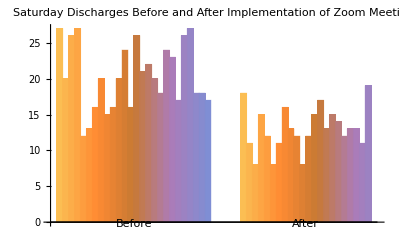

```mathematica
satBar = BarChart[{satPre2,satPost},BarSpacing->{0, 5},ChartLabels->{{"Before", "After"}, None}, PlotLabel->"Saturday Discharges Before and After Implementation of Zoom Meeting"]
```

```mathematica
weekendBar = BarChart[{preChange,postChange},BarSpacing->{0, 5},ChartLabels->{{"Before", "After"}, None}, PlotLabel->"Weekend Discharges Before and After Implementation of Zoom Meeting"]
```

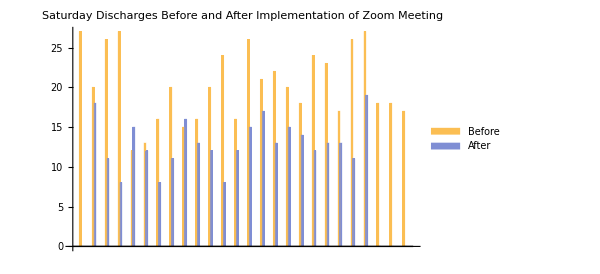

```mathematica
threadSat = BarChart[Transpose[{satPre2,PadRight[PadLeft[satPost, 23], 26]}],BarSpacing->{0, 5}, PlotLabel->"Saturday Discharges Before and After Implementation of Zoom Meeting", ChartLegends->{"Before", "After"}]
```

```mathematica
meanPre = Mean[preChange]
```

869/53

```mathematica
totalSTD = N[StandardDeviation[Join[preChange, postChange]]]
```

5.20258

```mathematica
preSTD  = StandardDeviation[preChange]
```

√(41729/1378)

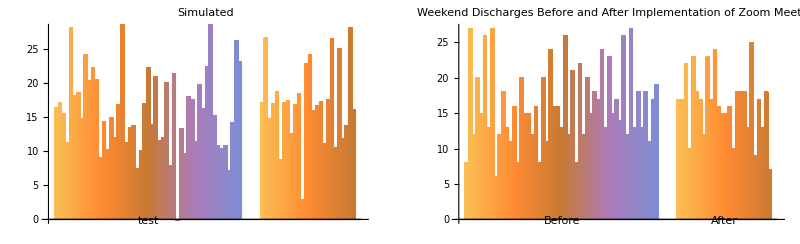

```mathematica
simPre = RandomVariate[NormalDistribution[meanPre, totalSTD], 51];
simPost = RandomVariate[NormalDistribution[meanPre+2, totalSTD], 26];
GraphicsRow[{BarChart[{Labeled[simPre, "test"], simPost},BarSpacing->{0, 5}, PlotRange->{0, 28}, PlotLabel-> "Simulated"], barReal}]
```

Generate this graph 8 times and plot it in a 2 by 4 grid

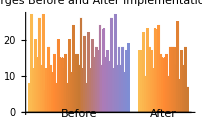
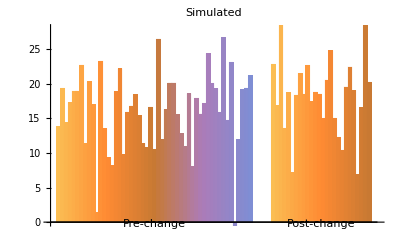
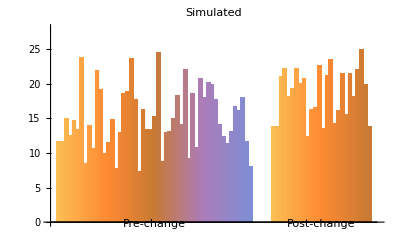
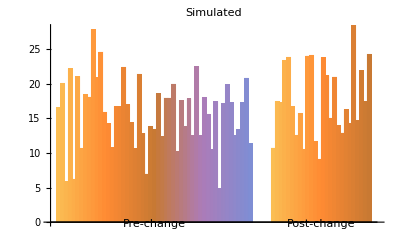
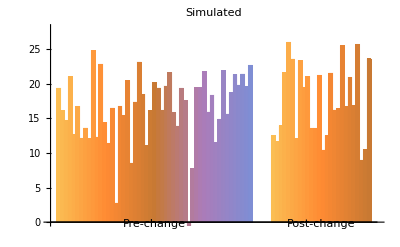
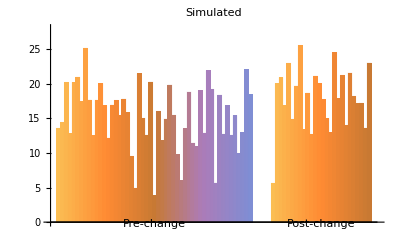
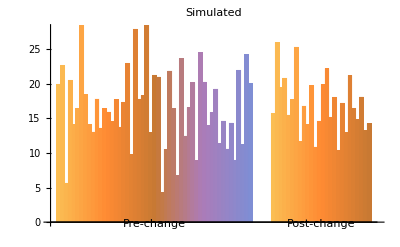
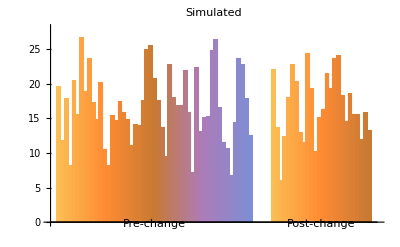

```mathematica
meanPre=49/3;
totalSTD=5.202582186629401;
delta = 1;
simulatedBars=Table[
    Module[{simPre,simPost},
        simPre=RandomVariate[NormalDistribution[meanPre,totalSTD],51];
        simPost=RandomVariate[NormalDistribution[meanPre+delta,totalSTD],26];
        BarChart[{Labeled[simPre, "Pre-change"],Labeled[simPost,"Post-change"] },BarSpacing->{0,5},PlotRange->{0,28},PlotLabel->"Simulated"]
    ],
    {11}
];
label = StringJoin["Simulated results if the mean of the post-change was ", ToString[delta]];
Prepend[simulatedBars, barReal]
(*GraphicsGrid[
    Partition[Prepend[simulatedBars, barReal],4], PlotLabel->label, Spacings->5
]*)
```

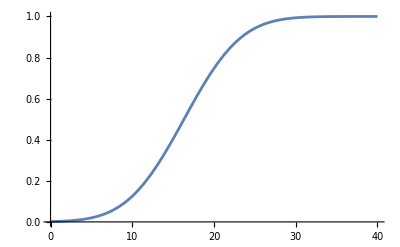

```mathematica
Plot[CDF[NormalDistribution[meanPre, preSTD], n], {n, 0, 40}]
```

```mathematica
preAround = Around[Join[missing23, preChange]]
```

```mathematica
postAround = Around[postChange]
```

```mathematica
Length[preChange]
```

```mathematica
Length[postChange]
```

```mathematica
N[preSTD]
```

```mathematica
BarChart[{Labeled[preAround, "Before"], Labeled[postAround, "After"]}, BarSpacing->2, PlotLabel->"Average Discharges Before and After 2/10/24"]
```

```mathematica
1666 / 104
```

```mathematica
mean23 = N[833/52]
```

```mathematica
data23 = Length[preChange] - 10
```

```mathematica
104 - 43
```

```mathematica
missing23 = RandomVariate[NormalDistribution[mean23, preSTD], 61]
```

```mathematica
Join[]
```